```mathematica
ko01100=Import[NotebookDirectory[]<>"data/ko01100.xml"][[2]][[3]];
hsa00230=Import[NotebookDirectory[]<>"data/hsa00230.xml"][[2]][[3]];
hsa00240=Import[NotebookDirectory[]<>"data/hsa00240.xml"][[2]][[3]];
hsa00250=Import[NotebookDirectory[]<>"data/hsa00250.xml"][[2]][[3]];
hsa00260=Import[NotebookDirectory[]<>"data/hsa00260.xml"][[2]][[3]];
hsa00330=Import[NotebookDirectory[]<>"data/hsa00330.xml"][[2]][[3]];
hsa00480=Import[NotebookDirectory[]<>"data/hsa00480.xml"][[2]][[3]];
```

```mathematica
metaDataList={hsa00230,hsa00250,hsa00260,hsa00330,hsa00480,ko01100};
metaDataJoined=Join[hsa00230,hsa00250,hsa00260,hsa00330,hsa00480,ko01100];
```

```mathematica
nodeList=Table[Association/@Cases[metaDataList[[i]],XMLElement["entry",attr_,_]:>attr,Infinity],{i,Length[metaDataList]}];
nodes=Association/@Cases[metaDataJoined,XMLElement["entry",attr_,_]:>attr,Infinity];
nodes=DeleteDuplicates[nodes[[All,"name"]]];
ruleID2KID=Table[Table[nodeList[[i]][[j]]["id"]->nodeList[[i]][[j]][["name"]],{j,Length[nodeList[[i]]]}],{i,Length[metaDataList]}];
```

```mathematica
RelationData=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr_,_],
XMLElement["product",productAttr_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr,"name",None]},"product"->{Lookup[productAttr,"name",None]}}],Infinity];
```

```mathematica
RelationDataDualSub=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr1_,_],
XMLElement["substrate",substrateAttr2_,_],
XMLElement["product",productAttr_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr1,"name",None],Lookup[substrateAttr2,"name",None]},"product"->{Lookup[productAttr,"name",None]}}],Infinity];
```

```mathematica
RelationDataDualPro=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr_,_],
XMLElement["product",productAttr1_,_],
XMLElement["product",productAttr2_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr,"name",None]},"product"->{Lookup[productAttr1,"name",None],Lookup[productAttr2,"name",None]}}],Infinity];
```

```mathematica
RelationDataDualSubDualPro=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr1_,_],
XMLElement["substrate",substrateAttr2_,_],
XMLElement["product",productAttr1_,_],
XMLElement["product",productAttr2_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr1,"name",None],Lookup[substrateAttr2,"name",None]},"product"->{Lookup[productAttr1,"name",None],Lookup[productAttr2,"name",None]}}],Infinity];
```

```mathematica
RelationDataTriSub=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr1_,_],
XMLElement["substrate",substrateAttr2_,_],
XMLElement["substrate",substrateAttr3_,_],
XMLElement["product",productAttr_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr1,"name",None],Lookup[substrateAttr2,"name",None],Lookup[substrateAttr3,"name",None]},"product"->{Lookup[productAttr,"name",None]}}],Infinity];
```

```mathematica
RelationDataDualSubTriPro=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr1_,_],
XMLElement["substrate",substrateAttr2_,_],
XMLElement["product",productAttr1_,_],
XMLElement["product",productAttr2_,_],
XMLElement["product",productAttr3_,_]
}
]
:>Association[{"reaction"->StringSplit[Lookup[attr,"name",None]],"type"->Lookup[attr,"type",None],"substrate"->{Lookup[substrateAttr1,"name",None],Lookup[substrateAttr2,"name",None]},"product"->{Lookup[productAttr1,"name",None],Lookup[productAttr2,"name",None],Lookup[productAttr3,"name",None]}}],Infinity];
```

```mathematica
NameAndReaction=Cases[metaDataJoined,XMLElement["entry",attr_,{___,XMLElement["graphics",{___,"name"->names_,___},___]}] /;Lookup[attr,"type"]=="gene":>Association[{"name"->StringSplit[Lookup[attr,"name",None]],"reaction"->StringSplit[Lookup[attr,"reaction",None]]}],Infinity];
```

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[None].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

```mathematica
RelationDataAll=DeleteDuplicates[Join[RelationData,RelationDataDualSub,RelationDataDualPro,RelationDataDualSubDualPro,RelationDataTriSub,RelationDataDualSubTriPro]];
```

```mathematica
ReactionDataAll=DeleteDuplicates[Map[Module[{reaction,substrate,product,type},
reaction="reaction"/.#;
substrate="substrate"/.#;
product="product"/. #;
type="type"/.#;
If[type==="irreversible",
<|"name"->Flatten@reaction,"reaction"->Flatten@Table[Flatten@Table[substrate[[i]]->product[[j]],{j,Length[product]}],{i,Length[substrate]}]|>,
<|"name"->Flatten@reaction,"reaction"->Flatten@Table[Flatten@Table[substrate[[i]]<->product[[j]],{j,Length[product]}],{i,Length[substrate]}]|>]]&,RelationDataAll]];
ReactionDataAllOneWay=DeleteDuplicates[Map[Module[{reaction,substrate,product,type},
reaction="reaction"/.#;
substrate="substrate"/.#;
product="product"/. #;
type="type"/.#;
If[type==="irreversible",
<|"name"->Flatten@reaction,"reaction"->Flatten@Table[Flatten@Table[substrate[[i]]->product[[j]],{j,Length[product]}],{i,Length[substrate]}]|>,
<|"name"->Flatten@reaction,"reaction"->Flatten@Table[Flatten@Table[substrate[[i]]->product[[j]],{j,Length[product]}],{i,Length[substrate]}]|>]]&,RelationDataAll]];
ReactionEdge=DeleteDuplicates@Flatten@DeleteDuplicates[Map[Module[{reaction,substrate,product,type},
reaction="reaction"/.#;
substrate="substrate"/.#;
product="product"/. #;
type="type"/.#;
If[type==="irreversible",
Flatten@Table[Flatten@Table[substrate[[i]]->product[[j]],{j,Length[product]}],{i,Length[substrate]}],
Flatten@Table[Flatten@Table[substrate[[i]]->product[[j]],{j,Length[product]}],{i,Length[substrate]}]]]&,RelationDataAll]];
```

```mathematica
Reaction2Gene=Flatten@Table[
((Association@Normal@Flatten@Select[ReactionDataAllOneWay,#name===nr["reaction"]&])[["reaction"]])[[1]]->nr["name"],{nr,NameAndReaction}];
```

```mathematica
(*edges=DeleteDuplicates[Map[Module[{substrate,product,type},
substrate="substrate"/. #;
product="product"/. #;
type="type"/. ("reaction"/. #);
If[type==="irreversible",substrate[[2]][[2]]->product[[2]][[2]],substrate[[2]][[2]]->product[[2]][[2]]]]&,RelationData]]*)
(*edgeList=Table[{Rule@@@RelationData[[i]][[All,{"entry1","entry2"}]]},{i,Length[metaDataList]}];
edges=Flatten[Table[edgeList[[i]]/.ruleID2KID[[i]],{i,Length[metaDataList]}]];*)
```

```mathematica
graph=Graph[nodes,ReactionEdge,GraphLayout->"GravityEmbedding"];
```

```mathematica
selectedData=Import[NotebookDirectory[]<>"data/mapData.csv","Dataset","HeaderLines"->1];
GeneData=Import[NotebookDirectory[]<>"data/final_data.csv","Dataset","HeaderLines"->1];
selectedNodes=Rest[selectedData[All,"ID"]];
prefixedselectedNodes= Normal[StringJoin["cpd:",#]&/@selectedNodes];(*ruleID2KID=Table[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&][[i]]["id"]->StringTake[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&][[i]]["name"],{5,-1}],{i,Length[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&]]}];*)
ruleKID2Label=Table[Normal[StringJoin["cpd:",Normal[selectedData][[i]][[1]]]]->Normal[selectedData][[i]][[4]],{i,Length[selectedData]}];
```

```mathematica
hsa2symbol=AssociationThread[Table[StringJoin["hsa:",ToString[#[[All,"kegg"]][[i]]]],{i,Length[#[[All,"kegg"]]]}],#[[All,"SYMBOL"]]]&@Normal@GeneData;
```

```mathematica
gene2express=AssociationThread[Table[StringJoin["hsa:",ToString[#[[All,"kegg"]][[i]]]],{i,Length[#[[All,"kegg"]]]}],Transpose[{#[[All,"human_log2FoldChange"]],#[[All,"mouse_log2FoldChange"]]}]]&@Normal@GeneData;
```

```mathematica
Reaction2Symbol=Reaction2Gene/.hsa2symbol;
```

```mathematica
Reaction2Symboloutput=Map[Rule[First[#],Select[Last[#],StringFreeQ[#,"hsa"]&]]&,Reaction2Symbol];
```

```mathematica
Reaction2Express= Reaction2Gene/.gene2express;
```

```mathematica
Mean@{{2.191712243,4.615341257},{-3.678754537,5.578160878},{-7.580623451,-5.294213306}}
```

{-3.02256,1.6331}

```mathematica
Reaction2Expressoutput=Map[ReplacePart[#,2->DeleteCases[#[[2]],_?(StringContainsQ[#,"hsa"]&)]]&,Reaction2Express];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[{0.0572395,-5.30581},hsa].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[{2.00789,-0.24853},hsa].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[{2.64131,2.73043},hsa].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

```mathematica
Reaction2ExpressMean=Table[If[Reaction2Expressoutput[[i]][[2]]!={},Reaction2Expressoutput[[i]][[1]]->Mean@Reaction2Expressoutput[[i]][[2]]],{i,Length[Reaction2Expressoutput]}]/. Null->Sequence[];
```

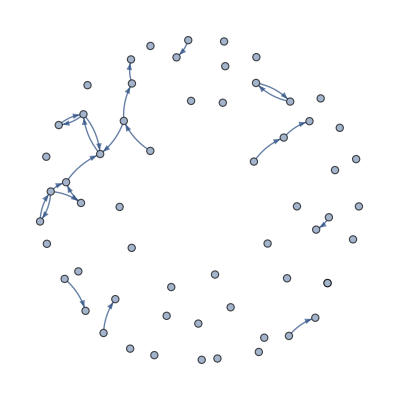

```mathematica
subgraph=Subgraph[graph,prefixedselectedNodes]
```

```mathematica
shortestPaths=Table[FindShortestPath[graph,prefixedselectedNodes[[i]],prefixedselectedNodes[[j]]],{i,Length[prefixedselectedNodes]},{j,i+1,Length[prefixedselectedNodes]}];
subgraphWithShortestPaths=Subgraph[graph,shortestPaths];
(*subgraph=FindSpanningTree[subgraphWithShortestPaths]*)
```

FindShortestPath::inv: The argument cpd:C00318 in FindShortestPath[Graph[<6638>, <3784>], cpd:C00018, cpd:C00318] is not a valid vertex.

FindShortestPath::inv: The argument cpd:C00670 in FindShortestPath[Graph[<6638>, <3784>], cpd:C00018, cpd:C00670] is not a valid vertex.

FindShortestPath::inv: The argument cpd:C02571 in FindShortestPath[Graph[<6638>, <3784>], cpd:C00018, cpd:C02571] is not a valid vertex.

General::stop: Further output of FindShortestPath::inv will be suppressed during this calculation.

```mathematica
Head@(Temp/.Reaction2ExpressMean)[[101]][[1]]
```

Part::partd: Part specification Temp⟦101⟧ is longer than depth of object.

Symbol

```mathematica
Head["cpd:C00018"]
```

String

```mathematica
Reaction2ExpressMean[[1]]
```

(cpd:C00035→cpd:C00361)→{0.0572395,-5.30581}

```mathematica
ColorMap=ColorData["ThermometerColors"];
name2CF[name_]:={Normal[
Select[selectedData,#ID==StringSplit[name,":"][[2]]&][[1,"humanFC"]]],Normal[
Select[selectedData,#ID==StringSplit[name,":"][[2]]&][[1,"mouseFC"]]]}
cfHeatmap[name_]:={ColorMap[name2CF[name][[1]]/10+0.5],ColorMap[name2CF[name][[2]]/10+0.5]}
vfHeatmap[{xc_,yc_},name_,{w_,h_}]:=If[name2CF[name]!={"#N/A","#N/A"} ,{cfHeatmap[name][[1]],Rectangle[{xc-2w*4/3,yc-h*4/3},{xc,yc+h*4/3}],cfHeatmap[name][[2]],Rectangle[{xc,yc-h*4/3},{xc+2w*4/3,yc+h*4/3}]},{Circle[{xc,yc},h]}]
cfHeatmap[{x_,y_}]:={ColorMap[x/10+0.5],ColorMap[y/10+0.5]};
(*Reaction2Heatmap[{x_,y_}]:=Block[{s=0.1},{cfHeatmap[{x,y}][[1]],Rectangle[{-s,-s},{s,s}],cfHeatmap[{x,y}][[1]],Rectangle[{-s,-s},{s,s}]}]*)
Reaction2Heatmap[reaction_,{x_,y_}]:=Graphics[Block[{s=1},{Text[(reaction/.Reaction2Symboloutput)[[1]],Scaled@{0,s}],EdgeForm[Thickness[Medium]],cfHeatmap[{x,y}][[1]],Rectangle[Scaled@{-2s,-s/2},Scaled@{0,s/2}],cfHeatmap[{x,y}][[2]],Rectangle[Scaled@{0,-s/2},Scaled@{2s,s/2}]}]]
Reaction2HeatmapRule=Table[Reaction2ExpressMean[[i]][[1]]->Reaction2Heatmap[Reaction2ExpressMean[[i]][[1]],Reaction2ExpressMean[[i]][[2]]],{i,Length[Reaction2ExpressMean]}];
(*efHeatmap[{xc_,yc_},name_,{w_,h_}]:=If[name2CF[name]!={"#N/A","#N/A"} ,{cfHeatmap[name][[1]],Rectangle[{xc-2w*4/3,yc-h*4/3},{xc,yc+h*4/3}],cfHeatmap[name][[2]],Rectangle[{xc,yc-h*4/3},{xc+2w*4/3,yc+h*4/3}]},{Circle[{xc,yc},h]}]*)
ef[pts_List, e_] := Block[{s = 0.03,E=(e[[1]]->e[[2]])},
 {
(*,{{cfHeatmap[E/.Reaction2ExpressMean][[1]],Rectangle[{2s,2s}+Mean@pts,Mean@pts]},{cfHeatmap[E/.Reaction2ExpressMean][[2]],Rectangle[Mean@pts,-{2s,-2s}+Mean@pts]}}*)
If[Head@(E/.Reaction2ExpressMean)[[1]]==Real,
{Text[E/.Reaction2Symboloutput,{0,2s}+Mean@pts],{cfHeatmap[E/.Reaction2ExpressMean][[1]],Rectangle[{2s,2s}+Mean@pts,Mean@pts]},{cfHeatmap[E/.Reaction2ExpressMean][[2]],Rectangle[Mean@pts,-{2s,-2s}+Mean@pts]},{Blend[cfHeatmap[E/.Reaction2ExpressMean]],{Arrowheads[s], Arrow[pts]}}}
],{Gray,Arrowheads[s], Arrow[pts]}
}]
subgraph=Graph[FindSpanningTree@subgraphWithShortestPaths,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label,EdgeShapeFunction->ef]
(*Output=GraphPlot[subgraph,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label,EdgeLabels->Reaction2Expressoutput]*)
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

{{0.0572395,-5.30581}}

```mathematica
Export[NotebookDirectory[]<>"output.svg",Graph[FindSpanningTree@subgraphWithShortestPaths,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label,EdgeShapeFunction->ef,ImageSize->{2048*10,2048}](*Graph[FindSpanningTree@subgraphWithShortestPaths,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label]*)]
```

/home/maxwell-gao/Documents/MappingMetabolism/output.svg